```mathematica
Bdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/B.csv"];
npdata=Import["/phys/users/mbuuck/Desktop/npsig.csv"];
pndata=Import["/phys/users/mbuuck/Desktop/pnsig.csv"];
σpndata=Union[npdata,pndata];
ϵpndata=Import["/phys/users/mbuuck/Desktop/pnepsilon.csv"];
```

```mathematica
Bmodel=LinearModelFit[Transpose[{Transpose[Bdata][[1]],Transpose[Bdata][[2]]}],x,x]
```

FittedModel[0.401428+1.29697 x]

```mathematica
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
m=938.272046(*Mega ElectronVolt*);
```

```mathematica
B[x_]=Bmodel["BestFit"];
```

```mathematica
γ[En_]=Sqrt[B[Sqrt[2*m/1000*En/1000]]]*(ℏc/1000);
```

```mathematica
γ[500]^2
```

0.0645486

```mathematica
σbf=BezierFunction[DeleteDuplicates[Log[σpndata],#1[[1]]==#2[[1]]&]]
```

BezierFunction[{{0.,1.}},<>]

```mathematica
Show[Graphics[{Red,Point[Log[σpndata]]},Axes->True],ParametricPlot[σbf[t],{t,0,1}]]
```

-Graphics-

```mathematica
σg=Interpolation[σbf/@Range[0,1,.001]]
```

InterpolatingFunction[{{-5.55968,5.9135}},<>]

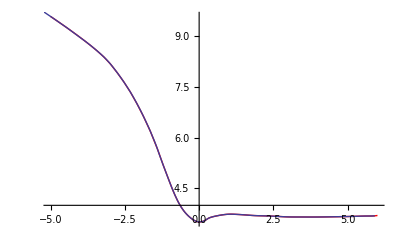

```mathematica
σp1=Plot[σg[x],{x,-5,6},PlotStyle->Red];
σp2=ParametricPlot[σbf[t],{t,0,1}];
Show[σp1,σp2]
```

```mathematica
σpn[En_]=Exp[σg[Log[Sqrt[2*m/1000*En/1000]]]];
```

```mathematica
σpn[2000]
```

40.4281

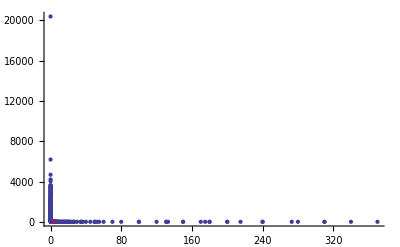

```mathematica
Show[ListPlot[σpndata],Plot[Exp[σg[Log[x]]],{x,.00385,7},PlotStyle->Red]]
```

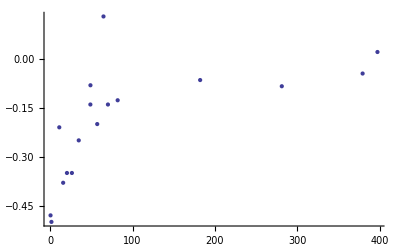

```mathematica
ListPlot[ϵpndata]
```

```mathematica
ϵbf=BezierFunction[DeleteDuplicates[ϵpndata,#1[[1]]==#2[[1]]&]]
```

BezierFunction[{{0.,1.}},<>]

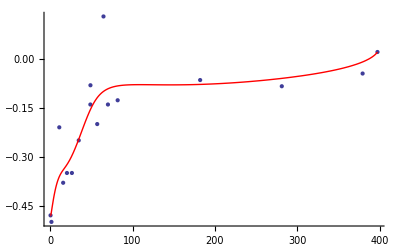

```mathematica
Show[ListPlot[ϵpndata],ParametricPlot[ϵbf[t],{t,0,1},PlotStyle->Red]]
```